```mathematica
$Assumptions:={r>0,r0>0,u>0,s>0,h>0,a>0,a>s, r<a, r0<a, r>s, r0>s, D>0,t>0,kf>0,n∈Integers,n>0,theta≥0,theta≤π, s∈Reals, h∈Reals}
```

```mathematica
params = {s -> 1, r0 -> 1, D -> 1, kf -> 160}
```

{s→1,r0→1,D→1,kf→160}

```mathematica
kD=4*Pi*D*s;
a=(1+kf/kD)*Sqrt[D]/s;
```

```mathematica
coeff[r_]:=1/(4*Pi*r*r0*Sqrt[D]);
term1[r_,t_]:=1/Sqrt[4*Pi*t]*Exp[-(r-r0)^2/(4*D*t)];
term2[r_,t_]:=1/Sqrt[4*Pi*t]*Exp[-(r+r0-2*s)^2/(4*D*t)];
w1[r_,t_]:=(r+r0-2*s)/Sqrt[4*D*t];
w2[t_]=a*Sqrt[t];
term3[r_,t_]:=a*Exp[2*w1[r,t]*w2[t]+w2[t]^2]*Erfc[w1[r,t]+w2[t]];

pirr[r_, t_]:= 4 Pi r r*coeff[r]*(term1[r,t]+term2[r,t]-term3[r,t]);
```

```mathematica
kirr[t_] := (kf / (kf+kD)) ( kD + kf Exp[ (a Sqrt[t])^2 ] Erfc[ a Sqrt[t]])
```

```mathematica
pirr[r,t]
```

(r ((ⅇ^(-(r-r0)^2/(4 D t)))/(2 √π √t)+(ⅇ^(-(r+r0-2 s)^2/(4 D t)))/(2 √π √t)-(√D ⅇ^((D (1+kf/(4 D π s))^2 t)/s^2+(√D (1+kf/(4 D π s)) (r+r0-2 s) √t)/(s √(D t))) (1+kf/(4 D π s)) Erfc[(√D (1+kf/(4 D π s)) √t)/s+(r+r0-2 s)/(2 √(D t))])/s))/(√D r0)

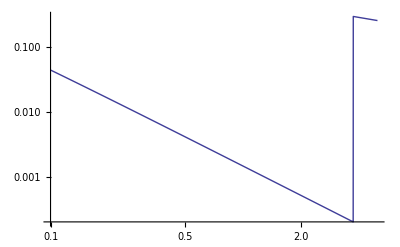

```mathematica
LogLogPlot[pirr[s,t]  /. params, {t,0.1,5}]
```

```mathematica
kirr[t] /. params
```

(160 (4 π+160 ⅇ^((1+40/π)^2 t) Erfc[(1+40/π) √t]))/(160+4 π)

```mathematica
Limit[kirr[t] , t->0]
```

kf

```mathematica
dk = D[kirr[t],t]
```

(kf (-(√D kf (1+kf/(4 D π s)))/(√π s √t)+(D ⅇ^((D (1+kf/(4 D π s))^2 t)/s^2) kf (1+kf/(4 D π s))^2 Erfc[(√D (1+kf/(4 D π s)) √t)/s])/s^2))/(kf+4 D π s)

```mathematica
Limit[dk, t->0, Direction -> -1]
```

-∞

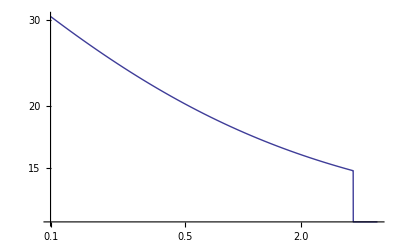

```mathematica
LogLogPlot[kirr[t] /. params, {t, 0.1, 5}]
```

```mathematica
Limit[Exp[x^2] Erfc[x], x->0]
```

1